```mathematica
a=Import["statproj.txt","Table"][[All,{1,2}]];
```

```mathematica
f[x_]=Fit[Select[a,(#[[1]]<20)&],{x,x^2,x^3,x^4},x]
```

19.8264 x+0.0515655 x^2-0.0105029 x^3+0.000150867 x^4

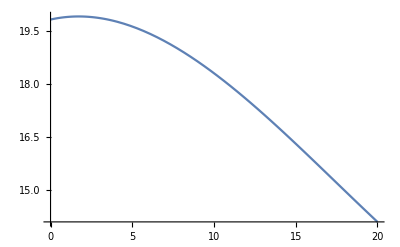

```mathematica
Plot[Evaluate[D[f[x],x]],{x,0,20}]
```

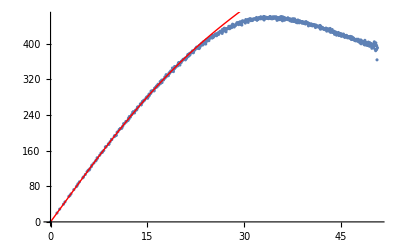

```mathematica
Show[
ListPlot[a,ImageSize->Scaled[1],PlotRange->All],
Plot[f[x],{x,0,Max[a[[All,1]]]},PlotStyle->{Thick,Red},PlotRange->All]
]
```

```mathematica
Show[
ListPlot[a,ImageSize->Scaled[1],PlotRange->All],
Plot[f[x],{x,0,Max[a[[All,1]]]},PlotStyle->{Thick,Red},PlotRange->All]
]
```

-Graphics-